# pH changes in localized electrolyte-electrode pair

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

## Spatio-temporal evolution of redox-active species

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory = NotebookDirectory[]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\

#### Phosphate Buffer equilibrium

Considering the equilibria of various ionic states of Phosphate buffer :

PO_4^-3+ H^+⇌HPO_4^-2 (K_1)

HPO_4^-2+ H^+⇌H_2 PO_4^- (K_2)

H_2 PO_4^-+ H^+⇌H_3 PO_4 (K_3)

Assuming the equilibria initially, we can calculate the initial concentration of all the species present in the system, using the equilibrium constants. Using the starting value of pH (7.0), we add H^+ with a constant rate given by the current flowing through the system. Assuming, initially total concentration was present as HPO_4

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[10 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"];
```

So, initial percent of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{1.72804×10^-6,0.386859,0.61313,8.6607×10^-6}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{1.72804×10^-8 M,0.00386859 M,0.0061313 M,8.6607×10^-8 M}

We can plot the concentration of various phosphate species in the droplet as a function of pH,

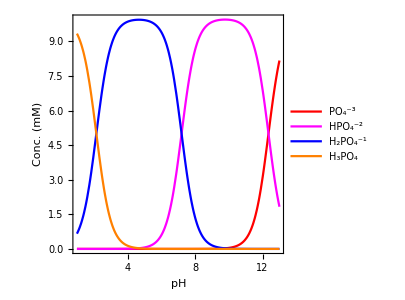

```mathematica
plot1=Plot[Evaluate[10^3{PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.Hp-> Quantity[10^-pH,"Molar"]],{pH,1,13},PlotLegends->Placed[LineLegend[{"PO_4^-3","HPO_4^-2","H_2PO_4^-1","H_3PO_4"},Spacings->0.2],{0.75,0.5}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,Frame-> True,FrameLabel->{"pH","Conc. (mM)"},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHConc.png",plot1,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHConc.png

Considering a constant flux of hydronium ions due to the redox reactions occurring at the electrode in the presence of the redox active species such as quinones (Current-Voltage relationship can be estimated using the staircase voltammetry). Assuming two electrons and protons taking part in the redox reaction, the rate of production of hydronium ions is given by,

ⅆH/ⅆt= J/(2F), So if we assume at time t, the amount of H^+added to the mixture is H^*, then we can write the equilibrium equations as,

PO_4^-3+ H^+⇌HPO_4^-2 (K_1)

(C_A- α H^*)                   (C_B+ α H^* - β H^*)

HPO_4^-2+ H^+⇌H_2 PO_4^- (K_2)

(C_B+ α H^* - β H^*)      (C_C+ β H^* - γ H^*)  

H_2 PO_4^-+ H^+⇌H_3 PO_4 (K_3)

 (C_C+ β H^* - γ H^*)              (C_D+ γ H^*)
 
 where C_A,C_B,C_C,C_D are the initial concentration of various species present initially (as calculated above), together with the constraint  α + β +γ  =1.

```mathematica
Clear[cA,cB,cC,cD]
```

```mathematica
eqnx1=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
```

```mathematica
eqnx2=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
```

```mathematica
eqnx3=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
```

```mathematica
eqnx4=α+β+γ ==1;
```

Eliminating α, β, γ and then solving H^+is must faster as compared to direct solving... but in principle both works..!

```mathematica
sol2=Solve[Eliminate[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ}], Hp];
```

```mathematica
sol3=Solve[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ, Hp}];
```

```mathematica
quant={cA-> icA,cB-> icB,cC-> icC,cD-> icD,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}/.q_Quantity:>QuantityMagnitude[q];
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"]/.q_Quantity:>QuantityMagnitude[q];
```

To check, if HpN → 0, we should recover the original equations, which are given by :

```mathematica
Chop[Hp/.sol2/.quant/.quant2/.HpN-> 0]
```

{-0.00197487,1.×10^-7,0}

Here, we consider all the calculations in SI units for simplicity,

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
dropletVolume=Quantity[2/3 π (0.5 10^-3)^3 ,"m^3"]; (* Considering a hemispherical droplet with radii 0.5 mm *)
```

```mathematica
(Quantity[5 10^-6,"Amperes"]Quantity[5,"s"])/(2 dropletVolume F)
```

0.494857 mol/m^3

```mathematica
hion[iC_,t_]=(Hp/.sol2⟦2⟧/.quant/.quant2/.HpN->10^-3 QuantityMagnitude[(iC t)/(2 dropletVolume F)]); (* A factor of thousand comes from conversion of moles/m^3 to Molar *)
```

```mathematica
Chop[hion[5 10^-6,0]]
```

1.×10^-7

Testing creation of protons by applying positive current (to estimate the voltage-time dependence, we can use experimentally derived current-voltage relationship)

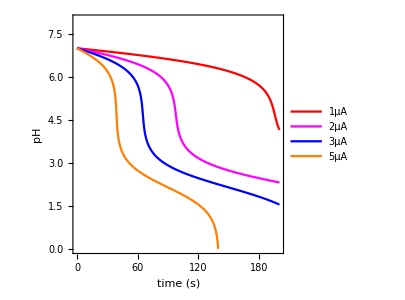

```mathematica
pHPlot1=Plot[{-Log[10,Chop@hion[1 10^-6,t]],-Log[10,Chop@hion[2 10^-6,t]],-Log[10,Chop@hion[3 10^-6,t]],-Log[10,Chop@hion[5 10^-6,t]]},{t,0,200},PlotRange-> {0,8},Frame-> True,FrameLabel-> {"time (s)","pH"},Exclusions-> None,PlotLegends->Placed[LineLegend[{"1μA","2μA","3μA","5μA"},Spacings->0.2],{0.15,0.15}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> {"1μA","2μA","3μA","5μA"},AspectRatio->1,ImageSize->300]
```

Instead of solving it analytically, we calculate numerically the pH as a function of applied current and temperature,

```mathematica
hion[iC_,t_]:=Hp/.NSolve[{Eliminate[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ}]/.{HpN->10^-3 QuantityMagnitude[(Quantity[iC,"Amperes"]Quantity[t,"s"])/(2 dropletVolume F)]}}/.quant,Hp,WorkingPrecision->Automatic] (* quant consists of initial concentrations of phosphate species, which makes pH=7 automatically *)
```

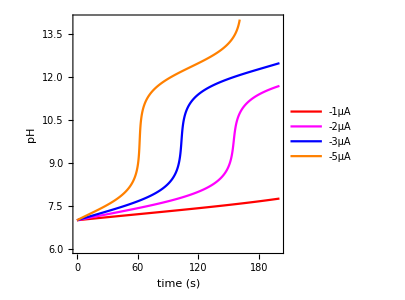

```mathematica
pHPlot2=ListPlot[{Table[{t,-Log[10,hion[-1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-5 10^-6,t]⟦3⟧]},{t,0,200,0.2}]},Joined-> True,PlotRange->{6,14},Frame-> True,FrameLabel-> {"time (s)","pH"},PlotLegends->Placed[LineLegend[{"-1μA","-2μA","-3μA","-5μA"},Spacings->0.2],{0.15,0.8}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHPlot1.png",pHPlot1,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHPlot1.png

```mathematica
Export[baseDirectory<>"pHPlot2.png",pHPlot2,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHPlot2.png

So, the numerical approach is more stable and works reliably for negative and positive currents.

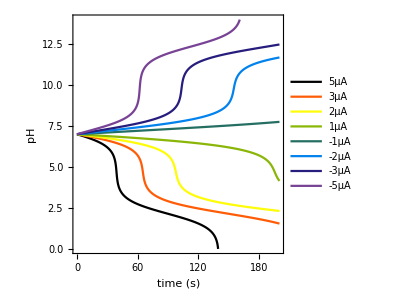

```mathematica
pHPlot=ListPlot[{Table[{t,-Log[10,hion[5 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-5 10^-6,t]⟦3⟧]},{t,0,200,0.2}]},Joined-> True,PlotRange->{0,14},Frame-> True,FrameLabel-> {"time (s)","pH"},PlotStyle->ColorData[3,"ColorList"],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> {"5μA","3μA","2μA","1μA","-1μA","-2μA","-3μA","-5μA"},ImageSize->300]
```

#### Calculating pH by time stepping current with defined time interval

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50; (* Setting the Machine Precision for stability while using NSolve *)
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Initial Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(2 dropletVolume F)];  
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

```mathematica
Quiet[pHdropletUpdate[ 1 10^-6,500,{icAM,icBM,icCM,icDM}]];(* Testing pH updating function *)
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[ 3 10^-6,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,0.01,200}],i]];
```

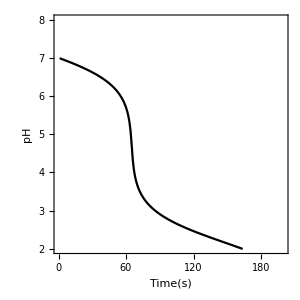

```mathematica
ListPlot[data⟦All,1⟧,PlotRange->{2,8},Joined-> True,PlotStyle->Black,PlotStyle-> Automatic,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"Time(s)","pH"},Frame->True,ImageSize->300]
```

Oscillating the current value for up to 10 cycles,

```mathematica
currentT =Flatten@Table[{ Table[-5 10^-6,{t,10}],Table[5 10^-6,{t,15}]},{i,10}];
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[currentT⟦i⟧,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[currentT]}],i]];
```

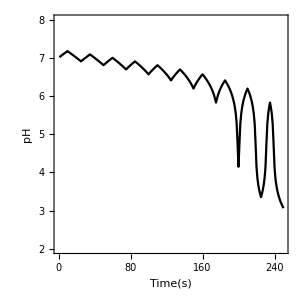

```mathematica
ListPlot[data⟦All,1⟧,PlotStyle->Black,PlotRange->{2,8},Joined-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

## Programmable pH changes together with control logic

Controls the pH inside the droplet using redox chemistry as described in the previous section, for programmable chemical reactions.

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
soln=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
soln//First
```

{PO4→(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),HPO4→(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),H2PO4→(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),H3PO4→(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
controlpH[pHValue_,initpH_,Δt_,totalPhosphate_,currentMag_,totalTime_]:= Module[{icA,icB,icC,icD,cA,cB,cC,cD,out,tSteps,currentPolarity,cCurrent,data},
(* 
   pHValue: pH value to be sustained,
   initpH: starting pH value,
   Δt: Time stepping for switching potentials,
   totalPhosphate: Total concentration of various phosphate species,
   currentMag: Magnitude of the applied current,
   totalTime: Total time of the simulation
*)
(* Calculating concentration of various phosphate species based on inital pH value *)
quant = {iHPO4-> Quantity[totalPhosphate,"Molar"],K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; 
quant2=Hp-> Quantity[10^-initpH,"Molar"];
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.soln/.quant/.quant2//Flatten; (* Initial variables *)
cA=icA;cB=icB;cC=icC;cD=icD; (* Time dependent variables *)
tSteps=IntegerPart@(totalTime/Δt);(* Total number of the steps *)
out={initpH,cA,cB,cC,cD};
data=Quiet[Monitor[Table[Block[{},
currentPolarity=If[out⟦1⟧>pHValue,1,-1];
out=pHdropletUpdate[currentPolarity currentMag,Δt,{cA,cB,cC,cD}];
cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,tSteps}],i]];data]
```

Trying to sustain certain pH using simple Finite State Logic at different applied currents.

```mathematica
dataF=Table[controlpH[9.,6.5,1.,5 10^-3,i 10^-6,300],{i,5,1,-1}];
```

```mathematica
Dimensions/@dataF
```

{{300,5},{300,5},{300,5},{300,5},{300,5}}

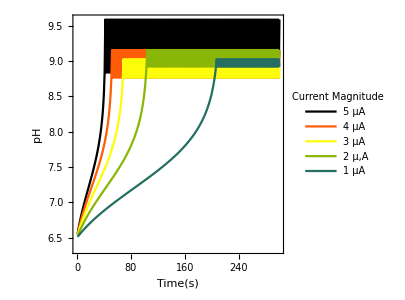

```mathematica
plot2=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,AspectRatio->1,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},PlotLegends->Placed[LineLegend[{"5 μA","4 μA","3 μA","2 μ,A","1 μA"},Spacings->0.2,LegendLabel->"Current Magnitude"],{0.75,0.23}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl1.png",plot2,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl1.png

Trying to sustain certain pH using simple Finite State Logic in the absence of dissipation and droplet-droplet coupling

```mathematica
dataF=Table[controlpH[i,6.5,1.,5 10^-3,2 10^-6,300],{i,2,12}];
```

```mathematica
Dimensions/@dataF
```

{{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5}}

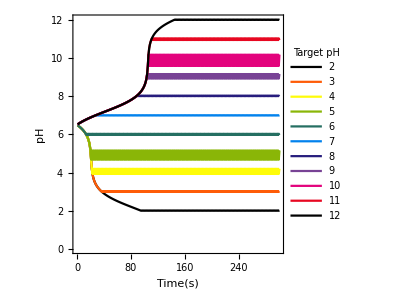

```mathematica
plot3=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,PlotLegends->Placed[LineLegend[Range[2,12],Spacings->0.1,LegendLayout->"Row",LegendLabel->"Target pH"],{0.5,0.08}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl2.png",plot3,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl2.png

Trying to sustain certain pH using simple Finite State Logic at different buffer concentrations  in the absence of dissipation and droplet - droplet coupling

```mathematica
dataF=Table[controlpH[9.,6.5,1.,i 5 10^-3,5 10^-6,600],{i,1,10}];
```

```mathematica
Dimensions/@dataF
```

{{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5}}

```mathematica
Table[ToString[i 5]<>" mM",{i,1,10}]
```

{5 mM,10 mM,15 mM,20 mM,25 mM,30 mM,35 mM,40 mM,45 mM,50 mM}

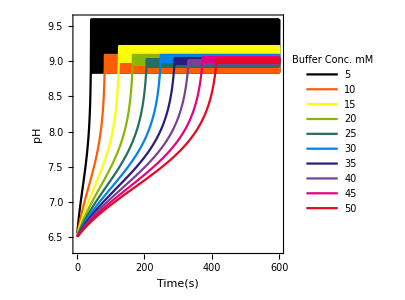

```mathematica
plot4=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,PlotLegends->Placed[LineLegend[Table[ToString[i 5],{i,1,10}],Spacings->0.2,LegendLayout->"Row",LegendLabel->"Buffer Conc. mM"],{0.55,0.15}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl3.png",plot4,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl3.png

## Two dimensional spatio-temporal dynamics in an array of localized electrolyte-electrode pairs

This section is similar to the one from the first part of the Mathematica notebook. Additionally to the previous version, we implement local pH changes due to the current flowing through the system in the presence of the buffered system, following the same dynamics as described in the previous section. As the current kinetics is simple and doesn’t allows the control over the number of species, we use higher buffered system, to the overall pH change within the droplet stays between the range 4-10 maximum.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\

#### Physical Constants

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]];(* Vacuum Permittivity *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

#### Basic design and chemistry parameters

```mathematica
elecRadius=UnitConvert@Quantity[1.0,"mm"]; (* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1.0,"mm"];(* Gap between two nearby electrodes *)
```

```mathematica
dropHeight=UnitConvert@Quantity[1.0,"mm"]; (* Height of the droplet above electrode array *)
```

```mathematica
dropletVolume = UnitConvert[(elecRadius+elecGap/2.)^2 dropHeight,"m^3"];(* Volume of the droplet based on the height and electrode dimensions *)
```

```mathematica
Cdl=UnitConvert@Quantity[0.02,"F/m^2"];(* Double Layer capacitance per unit area *)
```

```mathematica
CBack=UnitConvert@Quantity[300 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
𝒟=UnitConvert@Quantity[1 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[0.7 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity *)
```

2.25436 per meterper ohm

```mathematica
dropletBulkR1= 1/BulkCond elecGap/dropHeight^2
```

443.585 Ω

```mathematica
dropletBulkR = 1/BulkCond(2dropHeight)/elecGap^2
```

887.169 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

0.0000636547 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[ FullSimplify[j0[CEl,CEl,khom]],"A/m^2"]
```

24.1213 A/m^2

```mathematica
ExCurrentDensity/iLim
```

1.19048

#### Buffer Kinetics Parameters

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[30 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"];
```

So, initial percent of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{1.72804×10^-6,0.386859,0.61313,8.6607×10^-6}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{5.18411×10^-8 M,0.0116058 M,0.0183939 M,2.59821×10^-7 M}

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50;
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Initial Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(2 dropletVolume F)];  
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

```mathematica
Quiet[pHdropletUpdate[ 1 10^-4,20,{icAM,icBM,icCM,icDM}]];(* Testing pH updating function *)
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[5 10^-5,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,0.01,200}],i]];
```

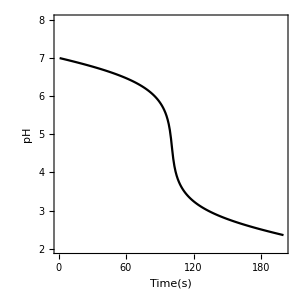

```mathematica
ListPlot[data⟦All,1⟧,PlotRange->{2,8},Joined-> True,PlotStyle->Black,PlotStyle-> Automatic,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,ImageSize->300]
```

#### Governing equations for multi-electrode array network

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ])
```

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
droplet2DmBV[i_,j_,K_,t0_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{0.01,t0},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0( (Exp[(αa F ηm)/(R T)]-Exp[-(αc F ηm)/(R T)])/(1+i0/iL(Exp[(αa F ηm)/(R T)]+Exp[-(αc F ηm)/(R T)])))/.ηm-> Evaluate[fVShift[{ Symbol["Vf"<>indexStr],Symbol["Vi"<>indexStr][t]},{0.01,t0},t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];
eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕP1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕP"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕP"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕP"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
λ=1 10^-4;
```

```mathematica
nEl=10;  (* Number of electrodes along X/Y *)
```

```mathematica
eqLen1=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,1⟧],Length[Union@dropletEndConnections2D[nEl]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,2⟧],Length[Union@dropletEndConnections2D[nEl]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2]
```

True

No. of variables 1320

```mathematica
{AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}
```

{AreaEL→3.14159×10^-6 m^2,RBulk→887.169 Ω,RBulkA→443.585 Ω,RBulkB→443.585 Ω,RConn→887.169 Ω,i0→24.1213 A/m^2,iL→20.2619 A/m^2,αa→0.5,αc→0.5,0.02 s^4 A^2/(kg m^4)→0.02,E0→0}

```mathematica
params={AreaEL->UnitConvert[ π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;(* Counter for electrode switching operations *)
tS=10; (* Time step for electrode switching *)
offSet=1.0; (* Offset time for setting up/down potential *)
Vapp={}; (* For saving applied electrode potentials *)
```

```mathematica
Clear[λ,tS]
```

```mathematica
offSet=0.5;λ=10^-4;vInit=0.25; (* Initial potential at time step 1*)
```

```mathematica
tS=2.5; (* Time stepping for changing electrochemical potential *)
```

```mathematica
electroChemAutomata[N_,time_,nTs_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
(* 
	N     : Number of electrodes in XY grid 
  time  : Total experimental time  
  nTS   : Total number of electrode switching time steps
Vinit : Bias potential on the electrodes at first time step.
*)
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;
Vapp={}; (* Keeping Applied Potentials *)
solnS={}; (* Keeping Solutions for variables *)
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
(* Updating electrode potentials *)
(* -> For the first step *)
If[cnTs==0,
(* -> Applying initial bias potential *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

(* -> For the generalized step *)
(*params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;*)
params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->RandomReal[{-1.0,1.0}]),{i,1,N},{j,1,N}]//Flatten; 
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
(* -> Applying initial conditions for t=0 *)
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
(* -> Applying initial conditions from previous switching step *)
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
(*Print[eqnsFF]//TableForm;*)
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];
cnTs=cnTs+1;]
];
```

```mathematica
nEl=6; (* Number of electrodes along X and Y *)
```

```mathematica
nTs=10; (* Number of switching steps *)
```

```mathematica
totTime=tS nTs ;(* Total simulation time *)
```

```mathematica
electroChemAutomata[nEl,totTime,nTs]
```

True

No. of variables 480

Current Switching Step: 0

Current Switching Step: 1

Current Switching Step: 2

Current Switching Step: 3

Current Switching Step: 4

Current Switching Step: 5

Current Switching Step: 6

Current Switching Step: 7

Current Switching Step: 8

Current Switching Step: 9

Current Switching Step: 10

Plotting : Applied potential, current at the electrode and the interface

```mathematica
{Dimensions[Vapp],Dimensions[solnS]}
```

{{11,2,36},{11,480}}

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-2.5,2.5}}][k]; (* Applied Potential *)
state[k_]:=ColorData[{"TemperatureMap",{-0.5 10^-3,0.5 10^-3}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"MintColors",{0,0.5 10^-3}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"GrayYellowTones",{0,1 10^3}}][k]; (* Electric Field Profile *)
state4[k_]:=ColorData[{"TemperatureMap",{0,14}}][k]; (* pH profile *)
```

```mathematica
BL1=BarLegend[{"TemperatureMap",{-2.5,2.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Applied Voltage (V)",LegendLayout->"Row"];
```

```mathematica
BL2=BarLegend[{"TemperatureMap",{-0.5,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Electrode Current(mA)",LegendLayout->"Row"];
```

```mathematica
BL3=BarLegend[{"MintColors",{0,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row"];
```

```mathematica
BL4=BarLegend[{"GrayYellowTones",{0,1 10^3}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row"];
```

```mathematica
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl];
Graphics[Flatten@Table[{stateV[plotV⟦i,j⟧],Disk[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Applied Potential",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC;
Graphics[Flatten@Table[{state[currentEL⟦i,j⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentCon[nEl_,tC_]:=Block[{cnT, time,dataPlot},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
Graphics[Table[{state2[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state2[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentVec[nEl_,tC_,color_]:=Block[{cnT, time,dataPlot},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;Graphics[Flatten@{color,If[dataPlot⟦#,3⟧≥0,Arrow[{{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧}}],Arrow[{{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧}}]]&/@Range[nEl^2],
If[dataPlot⟦#,4⟧≥0,Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45}}],Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45}}]]&/@Range[nEl^2]}]];
```

```mathematica
plotEFieldVec[nEl_,tC_]:=Block[{cnT, time,dataPlot,AreaF,connectArea,σ},
AreaF=0.3;
connectArea=AreaF QuantityMagnitude@UnitConvert[dropHeight^2,"m^2"];
σ=QuantityMagnitude@BulkCond;
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,1/σ 1/connectArea Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],1/σ 1/connectArea Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
Graphics[Flatten@{Table[{state3[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state3[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{Black,Circle[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}]},FrameTicks-> None,Frame-> True,PlotLabel->Text[Style["Electric Field Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,totTime,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{250,6,6}

```mathematica
Dimensions[dataC]
```

{6,6,250,5}

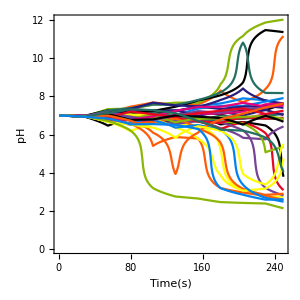

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,6},{j,1,6}],1],PlotRange-> Full,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->ColorData[3,"ColorList"],Frame->True,FrameLabel->{"Time(s)","pH"},Joined-> True,ImageSize->300]
```

```mathematica
plotpH[t_]:=Graphics[Flatten@Table[{state4[dataC⟦i,j,10t,1⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["pH Distribution",FontSize->14,FontColor->Black]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsGrid[Partition[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],Show[{plotEFieldVec[nEl,t],plotCurrentVec[nEl,t,Orange]}],plotpH[t]},2],Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]],ImageSize->600]
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_pH.png",plot[nEl,2],ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\ElectrodeArray_CV_pH.png

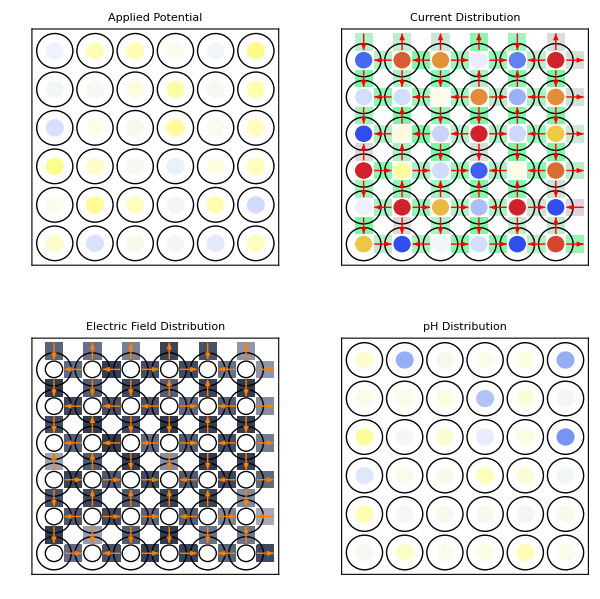

```mathematica
plot[nEl,18]
```

```mathematica
(* data=Table[plot[nEl,k],{k,1,25,0.1}]; *) (* Uncomment to make a gif *)
```

```mathematica
(* Export[baseDirectory<>"ElectrodeArray_CV_pH_2.gif",data] *) (* Uncomment to make a gif *)
```

In this section, we create electrode logic operations without the feedback from the chemical information processing.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.5;λ=10^-4;vInit=0.0;tS=2.5; (* Initial potential at time step 1 *)
```

```mathematica
electroChemAutomata[N_,time_,nTs_,potPatterns_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL->UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Print[params];
cnTs=0;Vapp={}; solnS={}; 
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
If[cnTs==0,
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]->0.0),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];cnTs=cnTs+1;]];
```

```mathematica
vInit=1. 10^-12;
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=-2.5;
potPatterns//MatrixForm
```

(1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | -2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | -2.5 | 2.5 | -2.5 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | -2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12)

```mathematica
electroChemAutomata[nEl,10,1,potPatterns]
```

True

No. of variables 335

{AreaEL→3.14159×10^-6,RBulk→887.169,RBulkA→443.585,RBulkB→443.585,RConn→887.169,i0→24.1213,iL→20.2619,αa→0.5,αc→0.5,0.02→0.02,E0→0}

Current Switching Step: 0

Current Switching Step: 1

```mathematica
Clear[dataC]
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,5,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{50,5,5}

```mathematica
Dimensions[dataC]
```

{5,5,50,5}

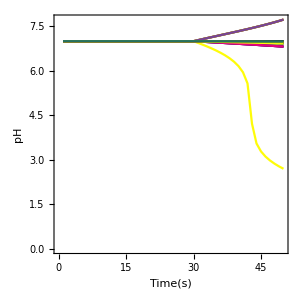

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,5},{j,1,5}],1],PlotRange-> Full,Joined-> True,PlotStyle->ColorData[3,"ColorList"],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-2.5,2.5}}][k]; (* Applied Potential *)
state[k_]:=ColorData[{"TemperatureMap",{-0.5 10^-4,0.5 10^-4}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"MintColors",{0,0.5 10^-4}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"GrayYellowTones",{0,1 10^3}}][k]; (* Electric Field Profile *)
state4[k_]:=ColorData[{"TemperatureMap",{4,11}}][k]; (* pH profile *)
```

```mathematica
plotpH[t_]:=Graphics[Flatten@Table[{state4[dataC⟦i,j,10t,1⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["pH Distribution",FontSize->14,FontColor->Black]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsGrid[Partition[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],Show[{plotEFieldVec[nEl,t],plotCurrentVec[nEl,t,Orange]}],plotpH[t]},2],Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]]]
```

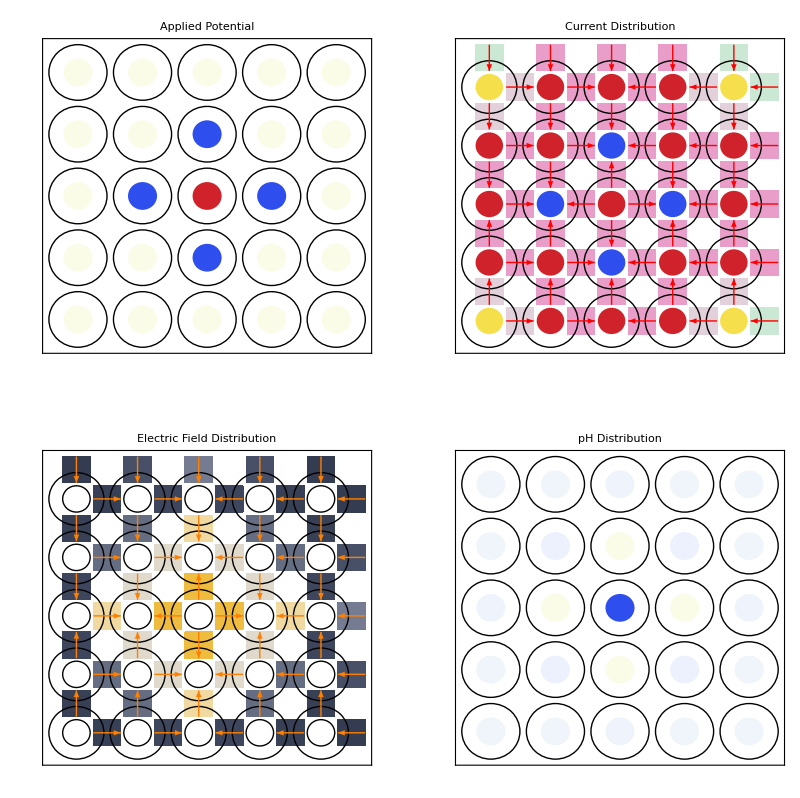

```mathematica
plot[nEl,4.5]
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=2.5;
potPatterns//MatrixForm
```

(1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 2.5 | -2.5 | 2.5 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12)

```mathematica
electroChemAutomata[nEl,10,1,potPatterns]
```

True

No. of variables 335

{AreaEL→3.14159×10^-6,RBulk→887.169,RBulkA→443.585,RBulkB→443.585,RConn→887.169,i0→24.1213,iL→20.2619,αa→0.5,αc→0.5,0.02→0.02,E0→0}

Current Switching Step: 0

Current Switching Step: 1

```mathematica
Clear[dataC]
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,5,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{50,5,5}

```mathematica
Dimensions[dataC]
```

{5,5,50,5}

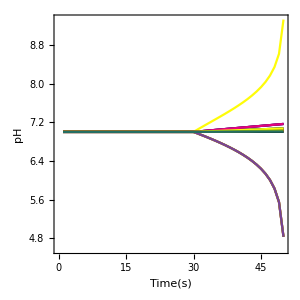

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,5},{j,1,5}],1],PlotRange-> Full,Joined-> True,AspectRatio->1,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

```mathematica
plot[nEl_,t_]:=GraphicsGrid[Partition[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],Show[{plotEFieldVec[nEl,t],plotCurrentVec[nEl,t,Orange]}],plotpH[t]},2],Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]]]
```

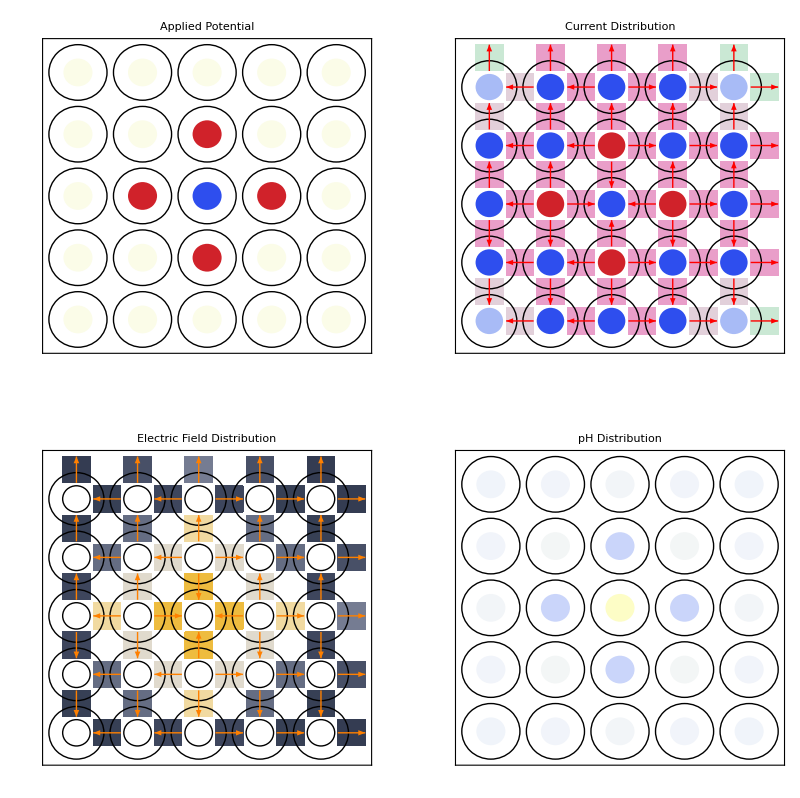

```mathematica
plot[nEl,4.5]
```

## Programmable pH changes with proportional logic : Single Working Electrode

In this section, we program pH changes over an electroactive arrays using proportional logic, with different control parameters. In this case, we will start with a minimalistic set of electrode arrays, and try to set different pHs over the electrodes.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=1.5; (* Time step for potential shift in seconds *) 
leakageCurrent = 1 10^-12; (* Leakage current on inactive electrodes in Amperes *)
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
appVoltage=1.5; (* Scaling factor for the applied voltage *)
αVoltage=0.25; (* Proportional factor for applied voltage based on pH difference *)
potPatterns=Table[vInit,{i,nEl},{j,nEl}]; (* Initial potential patterns *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
nElW =1; (* Number of working electrodes along X ans Y *)
```

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{5.18411×10^-8,0.0116058,0.0183939,2.59821×10^-7}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
WE={{3,3}};
```

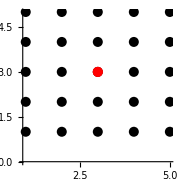

```mathematica
Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small]
```

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_,setpH_,αVoltage_,tS_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataT,Vapp,solnS,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
PrintTemporary[eqLen1== eqLen2];
PrintTemporary["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Clear[dim,pHdiffRec];
cnTs=0;Vapp={}; solnS={}; dataT={};pHdiffRec={};
(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;
setpHe=setpH; (* Setting the pH on the working electrode to be attained *)

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];

If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],PrintTemporary["****** SWITCHING TO NEW STATES ******"]];
PrintTemporary["Current pH states : ", setpHe];

Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];

dim=Dimensions[currentEL]; 
PrintTemporary[dim];
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
cnTs=cnTs+1];
Return[{Vapp,solnS,dataT}]];
```

```mathematica
cnTs=0;nSteps=30;
out1=electroChemAutomata[nEl,nSteps,4,0.1,1.0];
out2=electroChemAutomata[nEl,nSteps,4,0.2,1.0];
out3=electroChemAutomata[nEl,nSteps,4,0.3,1.0];
out4=electroChemAutomata[nEl,nSteps,4,0.4,1.0];
out5=electroChemAutomata[nEl,nSteps,4,0.5,1.0];
```

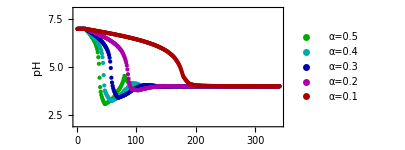

```mathematica
p11=ListPlot[Evaluate[{
Flatten@Table[Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{2,8}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},Spacings-> {0.1,0.1}],{0.85,0.65}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=30;
out1=electroChemAutomata[nEl,nSteps,4,0.1,2.5];
out2=electroChemAutomata[nEl,nSteps,4,0.2,2.5];
out3=electroChemAutomata[nEl,nSteps,4,0.3,2.5];
out4=electroChemAutomata[nEl,nSteps,4,0.4,2.5];
out5=electroChemAutomata[nEl,nSteps,4,0.5,2.5];
```

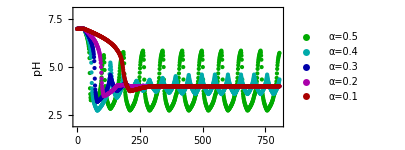

```mathematica
p12=ListPlot[Evaluate[{
Flatten@Table[Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{2,8}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=30;
out1=electroChemAutomata[nEl,nSteps,10,0.1,1.0];
out2=electroChemAutomata[nEl,nSteps,10,0.2,1.0];
out3=electroChemAutomata[nEl,nSteps,10,0.3,1.0];
out4=electroChemAutomata[nEl,nSteps,10,0.4,1.0];
out5=electroChemAutomata[nEl,nSteps,10,0.5,1.0];
```

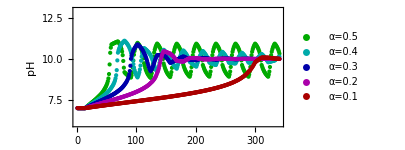

```mathematica
p21=ListPlot[Evaluate[{
Flatten@Table[Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{6,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=30;
out1=electroChemAutomata[nEl,nSteps,10,0.1,2.5];
out2=electroChemAutomata[nEl,nSteps,10,0.2,2.5];
out3=electroChemAutomata[nEl,nSteps,10,0.3,2.5];
out4=electroChemAutomata[nEl,nSteps,10,0.4,2.5];
out5=electroChemAutomata[nEl,nSteps,10,0.5,2.5];
```

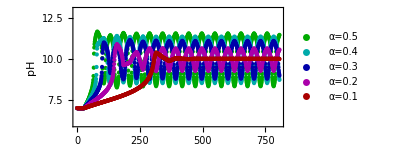

```mathematica
p22=ListPlot[Evaluate[{
Flatten@Table[Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],Flatten@Table[Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{6,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl_1.png",p11,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl_1.png

```mathematica
Export[baseDirectory<>"pHControl_2.png",p12,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl_2.png

```mathematica
Export[baseDirectory<>"pHControl_3.png",p21,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl_3.png

```mathematica
Export[baseDirectory<>"pHControl_4.png",p22,ImageResolution->300]
```

C:\Users\abhishek\Documents\Projects\Hybrid_Computation\Mathematica_Notebooks\pHControl_4.png

## Programmable pH changes with proportional logic : Multiple Working Electrodes

In this section, we program pH changes over an electroactive arrays using proportional logic, with different control parameters. In this case, we will start with a minimalistic set of electrode arrays, and try to set different pHs over the electrodes.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=1.5; (* Time step for potential shift in seconds *) 
leakageCurrent = 1 10^-12; (* Leakage current on inactive electrodes in Amperes *)
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
appVoltage=1.5; (* Scaling factor for the applied voltage *)
αVoltage=0.25; (* Proportional factor for applied voltage based on pH difference *)
potPatterns=Table[vInit,{i,nEl},{j,nEl}]; (* Initial potential patterns *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
nElW =1; (* Number of working electrodes along X ans Y *)
```

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{5.18411×10^-8,0.0116058,0.0183939,2.59821×10^-7}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
WE=Flatten[Table[{i,j},{i,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2},{j,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2}],1]
```

{{2,2},{2,4},{4,2},{4,4}}

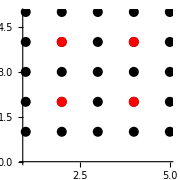

```mathematica
Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small]
```

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_,setpH_,αVoltage_,tS_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataT,Vapp,solnS,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
PrintTemporary[eqLen1== eqLen2];
PrintTemporary["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulk->dropletBulkR,RBulkA->dropletBulkR1,RBulkB->dropletBulkR1,RConn->dropletBulkR,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> 0.02,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Clear[dim,pHdiffRec];
cnTs=0;Vapp={}; solnS={}; dataT={};pHdiffRec={};
(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;
setpHe=setpH; (* Setting the pH on the working electrode to be attained *)

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];

If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],PrintTemporary["****** SWITCHING TO NEW STATES ******"]];
PrintTemporary["Current pH states : ", setpHe];

Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];

dim=Dimensions[currentEL]; 
PrintTemporary[dim];
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
cnTs=cnTs+1];
Return[{Vapp,solnS,dataT}]];
```

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.01],Length@WE],ConstantArray[Opacity[0.4],Length@WE],ColorData[16,#]&/@Range[Length@WE]}];
```

```mathematica
cnTs=0;nSteps=250;
out1=electroChemAutomata[nEl,nSteps,{4,4,8,8},0.1,1.0];
```

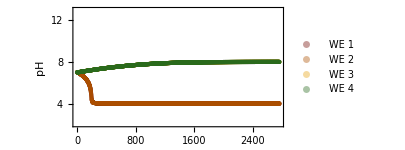

```mathematica
p1=ListPlot[Table[Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{2,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->plotStyle,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.1}],ImageSize->300]
```

```mathematica
Vapp=out1[[1]];plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0,100,0.1}];
```

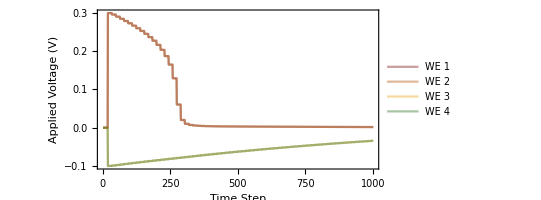

```mathematica
ListPlot[Evaluate[voltageData[[All,#[[1]],#[[2]]]]&/@WE],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time Step","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.6,0.9}],ImageSize->400]
```

```mathematica
cnTs=0;nSteps=100;
out2=electroChemAutomata[nEl,nSteps,{4,6,9,11},0.25,3.0];
```

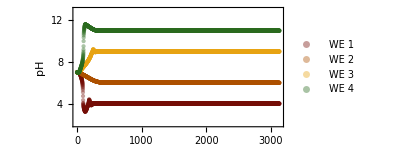

```mathematica
p2=ListPlot[Table[Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,Length@WE}],AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time Step","pH"},PlotRange-> {All,{2,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->plotStyle,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.1}],ImageSize->300]
```

```mathematica
Vapp=out2[[1]];plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0,30,0.1}];
```

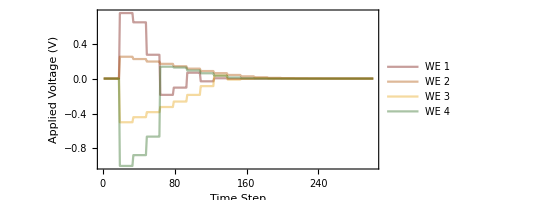

```mathematica
ListPlot[Evaluate[voltageData[[All,#[[1]],#[[2]]]]&/@WE],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time Step","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.6,0.9}],ImageSize->400]
```